# Sod’s Shock Tube (Analytical vs Numerical)

## Initial Conditions and Physics

```mathematica
Subscript[x, 1] = 0;
Subscript[x, 5] = 1;
Subscript[x, mid]= (Subscript[x, 1]+Subscript[x, 5])/2;
Subscript[ρ, 1] = 1.0;
Subscript[ρ, 5] = 0.125;
Subscript[P, 1] = 1.0;
Subscript[P, 5] = 0.1;
Subscript[v, 1]=0;
Subscript[v, 5]=0;
γ = 1.4;
Γ = (γ-1)/(γ+1);
β = (γ-1)/(2*γ);
Subscript[c, 1] = Sqrt[γ * Subscript[P, 1]/Subscript[ρ, 1]];
Subscript[c, 5] = Sqrt[γ * Subscript[P, 5]/Subscript[ρ, 5]];
```

## Analytical Solution

```mathematica
Subscript[P, 4] = Subscript[P, 3];
Subscript[u, 4f][p_]:= (p-Subscript[P, 5]) * Sqrt[(1-Γ)/(Subscript[ρ, 5]*(p + Γ*Subscript[P, 5]))]
Subscript[u, 3f][p_]:= (-p^β+(Subscript[P, 1])^β) * Sqrt[(1-Γ^2)*Subscript[P, 1]^(1/γ)/( Γ^2*Subscript[ρ, 1])]
Subscript[P, 3]=x/.FindRoot[Subscript[u, 4f][x]-Subscript[u, 3f][x],{x,0}];
Subscript[P, 4] = Subscript[P, 3];
Subscript[ρ, 3] = Subscript[ρ, 1](Subscript[P, 3]/Subscript[P, 1])^(1/γ);
Subscript[ρ, 4]= Subscript[ρ, 5]*(Subscript[P, 4]+Γ*Subscript[P, 5])/(Subscript[P, 5]+Γ*Subscript[P, 4]);
Subscript[u, 3] = Subscript[u, 4]= Subscript[u, 4f][Subscript[P, 3]];
Subscript[u, shock] = Subscript[v, 5]+Subscript[c, 5]*Sqrt[(γ-1+Subscript[P, 3]*(γ+1))/(2*γ)];
Subscript[u, contact]= Subscript[v, 1]+2*Subscript[c, 1]/(γ-1)*(1-(Subscript[P, 3]*Subscript[P, 5]/Subscript[P, 1])^((γ-1)/(2*γ)));
Subscript[X, 3][t_]:=Subscript[x, mid]+Subscript[u, 3] * t
Subscript[X, 4][t_]:=Subscript[x, mid]+(Subscript[u, 4]+Subscript[u, shock]) * t
Subscript[X, 1][t_]:=Subscript[x, mid]-Subscript[c, 1]*t
Subscript[X, 2][t_]:=Subscript[x, mid]+(-Subscript[u, 3]+Subscript[u, shock]) * t
time = 0.2;
Subscript[u, 2]=2/(γ+1)*(Subscript[c, 1]+(Subscript[X, 2][time]-Subscript[x, mid])/time);
Subscript[ρ, 2]=Subscript[ρ, 1]*(1−(γ−1)/2*Subscript[u, 2]/Subscript[c, 1])^(2/(γ−1));
```

## Numerical Simulation (Observe the dispersion)

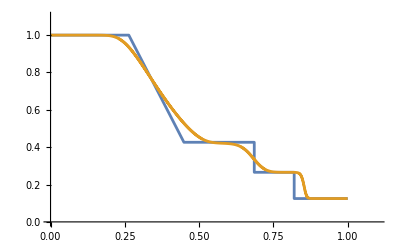

```mathematica
FileLines = Import["/home/francisco/Desktop/Euler-Equations-tests/Sod's Shock Tube/solutionSodShockTube.txt", "Data"];
DataPoints={};
For[i=1, i<Length[FileLines],i++,
AppendTo[DataPoints,{FileLines[[i]][[1]],FileLines[[i]][[2]]}];
]
ListLinePlot[{{{Subscript[x, 1],Subscript[ρ, 1]},{Subscript[X, 1][time],Subscript[ρ, 1]},{Subscript[X, 2][time],Subscript[ρ, 3]}, {Subscript[X, 3][time],Subscript[ρ, 3]},{Subscript[X, 3][time],Subscript[ρ, 4]},{Subscript[X, 4][time],Subscript[ρ, 4]},{Subscript[X, 4][time],Subscript[ρ, 5]},{Subscript[x, 5],Subscript[ρ, 5]}},DataPoints}, PlotRange->{{0,1.1},{0,1.1}}]
```